# Answers to Exercises Gaurav Kewalramani

# Week 3

## Q1)

for 2 small numbers :

```mathematica
m = 10
```

10

```mathematica
a = 3
```

3

```mathematica
EulerPhi[m]
```

4

```mathematica
PowerMod[a,EulerPhi[m],m]
```

1

```mathematica
GCD[m,a]
```

1

// 2 numbers are large

```mathematica
m= 12345
```

12345

```mathematica
a= 11111
```

11111

```mathematica
EulerPhi[m]
```

6576

```mathematica
PowerMod[a,EulerPhi[m],m]
```

1

```mathematica
GCD[m,a]
```

1

## Q2)

```mathematica
a = 861
```

861

```mathematica
b = 1645
```

1645

```mathematica
GCD[861,1645]
```

7

```mathematica
ExtendedGCD[a,b]
```

{7,{107,-56}}

// here GCD is 7 and the multipliers are 107 and -56. We have to show that recombining the multipliers with the two original numbers yields the GCD. 
So, we’ll say that x = 107 and y = -56. THEN a*x + b*y = GCD of (a,b)

```mathematica
x= 107
```

107

```mathematica
y = -56
```

-56

```mathematica
a*x + b*y
```

7

// here we can see that a*x + b*y is giving us 7 which was the GCD of (a,b). Hence proved.

## Q3)

// in the question we are given that x equivalent or ≡ 10(mod13), 5(mod29) and 7(mod64) and we have to find that Chinese remainder acting on [10,5,7] will give the same result as 10u1 + 5u2 + 7u3 mod 13*29*64

lets suppose M is the product of all the moduli i.e 13*29*64 then M1 = M/13, M2 = M/29 and M3 = M/64.

and then we know that u1 is inverse of M1(mod13) , u2 will be M2(mod29) similarly M3 which can be found using the powermod function 

then after finding u1,u2 and u3 we can find the result of 10u1 + 5u2 + 7u3 mod 13*29*64

```mathematica
M = 13*29*64
```

24128

```mathematica
M1 = 24128/13
```

1856

```mathematica
M2 = 24128/29
```

832

```mathematica
M3 = 24128/64
```

377

```mathematica
u1 = PowerMod[M1,-1,13]
```

4

```mathematica
u2 = PowerMod[M2,-1,29]
```

16

```mathematica
u3 = PowerMod[M3,-1,64]
```

9

```mathematica
Mod[(10*M1*u1 + 5*M2*u2 + 7*M3*u3),M]
```

19783

//here we can see that 10u1 + 5u2 + 7u3 mod 13*29*64 gives us the answer of 19783. 
Now we can check this by using the ChineseRemainder function.

```mathematica
ChineseRemainder [{10,5,7}, {13,29,64}]
```

19783

//Hence proved.

## Q4)

// The Diffie-Hellman key exchange involves two parties (commonly called Alice and Bob) who want to securely share a secret key. They each select private values and exchange derived public values, which allows them to compute a shared secret without directly transmitting it. Lets say p = 104729 and g = 2

Alice chooses a private key called a which is 56789. then her public key value will be A = g^a mod p, which when calculated will give us 2^56789 mod 104729 = 8836. So, A = 8836   

Now, Bob chooses a private key b which is 12345, then his public value B = g^b mod p, which when calculated will give us 5^12345 mod 104729 = 29455, So B = 29455.

Alice sends her public value A=8836 to Bob. and Bob send public Value B = 29455 to alice.

alice calculates secret key S using Bob’s public value as B^a mod p, then S = 29455^56789 mod 104729 = 30075, hence S = 30075. Similarly Bob do the same, for Bob S = A^b mod p. i.e 8836^12345 mod 104729 = 30075.

Since both Alice and Bob independently computed the same shared secret S=30075, they now have a common secret key that they can use for encrypted communication.

```mathematica
p =104729
```

104729

```mathematica
g=2
```

2

// alice chooses a private key and then computes her public value.

```mathematica
a = 56789
```

56789

```mathematica
A = PowerMod[g,a,p]
```

8836

//now bob does the same, he chooses a private key and then computes his public value.

```mathematica
b =12345
```

12345

```mathematica
B = PowerMod[g,b,p]
```

29455

//alice now calculates the shared secret key using Bob’s public value B and then Bob does the same with alice public value.

```mathematica
S1 = PowerMod [B,a,p]
```

30075

```mathematica
S2 = PowerMod[A,b,p]
```

30075

// we see S1 and S2 are equal, they both yield the same shared secret key.

## Q5)

// The ElGamal public key cryptosystem is an asymmetric encryption system that builds on the Diffie-Hellman key exchange principles. It provides a method for secure communication by allowing someone to encrypt a message using a recipient’s public key, where only the recipient can decrypt it using their private key. 

this usually works in 3 steps, 1st is key generation and then 2nd is encryption of a message for Bob and the 3rd is decryption of the message by bob 


Key Generation: We select a prime p and a primitive root a . The private key mB is chosen randomly, and the public key cB is computed as a^mB mod p, In the example given in the van Tilborg they have used the same example that they used for diifie hellman there they had p = 197 and a = 2 so cB was PowerMod[2,111,197].

Encryption: A random integer r is chosen. The ciphertext consists of two parts: R = a^r mod p and S = u * cB^r mod p, where u is the message.

Decryption: The recipient uses their private key mB which is 111  to compute s = a^mB mod p. The original message m is recovered by calculating m = S * s^(-1) mod p. ( here s = PowerMod[a,mB,p] )

```mathematica
p =197
```

197

```mathematica
a=2
```

2

// mB a private key chosen randomly by bob

```mathematica
mB =111
```

111

// cB is public value which is calculated using the private key just as in diffie hellman by bob

```mathematica
cB = PowerMod[a,mB,197]
```

82

// r is the random integer chosen by alice

```mathematica
r = RandomInteger[{0,p-2}]
```

189

// u here is the encrypted message

```mathematica
u =123
```

123

// Alice sends the pair (R,S) computed by :

```mathematica
R = PowerMod[a,r,p]
```

177

```mathematica
S = Mod[PowerMod[cB,r,197]u,p]
```

181

// To decrypt, Bob computes S/R^m_B mod p with his own secret m_B=111 by means of the Mathematica functions Mod and PowerMod.

```mathematica
Mod[S*PowerMod[PowerMod[R,mB,p],-1,p],p]
```

123

// The security of the ElGamal cryptosystem relies on the difficulty of the discrete logarithm problem, which is the problem of finding the exponent mB given a, cB, and p

## Q6)

// this part is called signing of the message by Alice. Suppose that Alice wants to send a signed message u to Bob. The message is again represented by an integer u 
Alice selects a random integer r that is relatively prime to p -1 and computes R = a^r
Next, Alice uses her secret exponent mA to compute S satisfying
u ≡ mA*R + r*S(mod p -1 ) 
Alice can use the extended version of euclid algorithm  to find S efficiently.
Alice sends to Bob the triple (u,R,S) where the pair (R,S) serves as signature on the message u.

Verification of the signature by Bob. Now Bob receives the triple (u,R,S) where u is the message and R,S is the signature. Here bob checks this signature R,S by verifying that a^u =  ( (cA)^R )  *( R^s * (mod p) ). 

now what we can do is replace the u in a^u with the steps alice did above and we’ll see that this relation holds.

lets suppose p = 197 and a = 2, they private key alice chose is mA = 56 and after solving for public value for alice we get cA = 178.
The message alice wants to sign is u  = 123, r be the random integer which is chosen by alice just like in the above example. then,

```mathematica
p =197
```

197

```mathematica
a=2
```

2

private key chosen by alice

```mathematica
mA = 56
```

56

calculation of public value.

```mathematica
cA = PowerMod[a, mA,197]
```

178

a random integer chosen by alice

```mathematica
r = 97
```

97

message to be sent

```mathematica
u =123
```

123

// calculation for R

```mathematica
R= PowerMod[a,r,197]
```

98

// calculation of S, could have also used the method used in the book i.e S/.Solve[{r S==u-mA *R},{S},Modulus->p-1][[1]], but went ahead with using Euclid’s algorithm here cause it was easy to understand and explain.

```mathematica
S=Mod[(u-mA*R)*PowerMod[r,-1,p-1],p-1]
```

171

// here value of R and S is 98 and 171 respectively. so alice adds R,S to the message U and sends it to Bob and bob checks this by verifying α^u≡(c_A)^R R^S (mod p):

```mathematica
PowerMod[a,u,p]==Mod[ PowerMod[cA,R,p]*PowerMod[R,S,p],p]
```

True

## Q7)

// RSA (Rivest-Shamir-Adleman) is a widely used public-key cryptosystem that relies on the mathematical properties of large prime numbers. The main steps in RSA are key generation, encryption and decryption.

I’m gonna explain the RSA steps as I’ll solve for the prime numbers

Choose two prime numbers p and q.

```mathematica
p =61
```

61

```mathematica
q = 53
```

53

// now we calculate n i.e p*q

```mathematica
n = q*b
```

654285

//Calculate the totient ϕ(n)=(p−1)(q−1) which can be done by using EulerPhi

```mathematica
phi = EulerPhi[n]
```

341952

// Choose a public exponent e such that 1<e<ϕ(n) and gcd (e,ϕ(n))=1.

```mathematica
e=RandomInteger[{1,n}];
While[GCD[e,phi]≠1,e=RandomInteger[{1,n}]];
e
```

423811

// here we calculated e as 423811, mind every time you re run this will give a different e to get a fixed value of just set e and check that 1<e<ϕ(n) and gcd (e,ϕ(n))=1. and you’ll be good with that. Now we have to calculate d, to do that we can either use extended GCD and when we get the two multipliers just take the one that correspond to dB or we can use the power mod function too cause d⋅e ≡ 1modϕ(n). so having this info we can easily calculate d, I’ve explained both steps below.

```mathematica
ExtendedGCD[e,phi]
```

{1,{-110741,137251}}

```mathematica
d=PowerMod[e,-1,phi];
```

```mathematica
d
```

231211

// so e = 330979 and d = 97291 and this can be checked by mod calculation, if we get one that means we are right.

```mathematica
Mod[e*d,phi]
```

1

// now we have checked it we can proceed  to write the public and the private keys

```mathematica
publicKey={e,n}
```

{423811,654285}

```mathematica
privateKey={d,n}
```

{231211,654285}

// now suppose we have a message m = 42

```mathematica
m = 42
```

42

then the encryption can be done by :

```mathematica
ciphertext=PowerMod[m,e,n]
```

171978

// and the decryption can be done by :

```mathematica
decryptedMessage=PowerMod[ciphertext,d,n]
```

42

//hence the cypher text here is 171978 and decryptedMessage is 42 we can also use chinese remainder to make our work a bit easier but it was no where mentioned that we have to use that to explain encryption and decryption so I just did it the basic way.

## Q8)

// the very thing here is that both alice and bob will have their RSA key pair consisting of public and private key. the steps of getting that private and public key for both of them will be exactly the same as above, soI’m not gonna explain again how to get those values.

// first we’ll calculate for alice

```mathematica
pAlice=61
qAlice=53
nAlice=pAlice*qAlice
phiAlice=EulerPhi[nAlice]
eAlice=17
dAlice=PowerMod[eAlice,-1,phiAlice]
publicKeyAlice={eAlice,nAlice} 
privateKeyAlice={dAlice,nAlice}
```

61

53

3233

3120

17

2753

{17,3233}

{2753,3233}

// now we’ll calculate for bob

```mathematica
pBob=67
qBob=59
nBob=pBob*qBob
phiBob=EulerPhi[nBob]
eBob=19
dBob=PowerMod[eBob,-1,phiBob]
publicKeyBob={eBob,nBob}
privateKeyBob={dBob,nBob}
```

67

59

3953

3828

19

403

{19,3953}

{403,3953}

// Alice will sign the message using her private key. Let’s assume the message m is represented as a number (in practice, the message would be hashed first).

```mathematica
message=42

signature=PowerMod[message,dAlice,nAlice]
```

42

3065

// Now Alice encrypts both the message and signature using Bob’s public key, ensuring only Bob can decrypt it.

```mathematica
encryptedMessage=PowerMod[message,eBob,nBob]       
encryptedSignature=PowerMod[signature,eBob,nBob]
```

3594

714

// now when Bob receives the encrypted message and signature, he decrypts them using his private key.

```mathematica
decryptedMessage=PowerMod[encryptedMessage,dBob,nBob]
decryptedSignature=PowerMod[encryptedSignature,dBob,nBob]
```

42

3065

//bob now verifies the signature by checking if the decrypted signature, when raised to Alice’s public exponent  eAlice, matches the decrypted message. if this returns true that means that verification is successful

```mathematica
isSignatureValid=PowerMod[decryptedSignature,eAlice,nAlice]==decryptedMessage
```

True

# Week 4

## Q1)

// in the book the syntax was given by ImplicitPlot but now we don’t use that we use contour plot, it was also told to add am Epilog ->Line, as the coefficient of x varies from -5 to -3. it was also told in the assignment to add Manipulate to add the line, I’ve tried to make a line in the plot without using it, it was working fine but the assignment asked to add that specific function.

```mathematica
elliptic=ContourPlot[y^2==x^3-5 x+3,{x,-3,3},{y,-4,4},Axes->True,Epilog->{Line[{{-3,4},{4,-3}}]}]
```

## Q2)

// When we substitute the line equation into the elliptic curve equation, we obtain a cubic equation in x. By the Fundamental Theorem of Algebra, this cubic equation has exactly three roots, which correspond to three intersection points but sometimes, a line might touch the curve at a single point, in which case that intersection point is counted multiple times. I can explain that by stating the example. If a line is tangent to the curve, it intersects at exactly one point with multiplicity 3 and If a line intersects the curve at two points (with one point being a tangent), it still counts as intersecting the curve three times.

```mathematica
ContourPlot[y^2==x^3-3 x+3,{x,-3,3},{y,-4,4},Axes->True,Epilog->{Line[{{-3,4},{4,-3}}]}]
```

with the same Epilog but with coefficient of x as -3

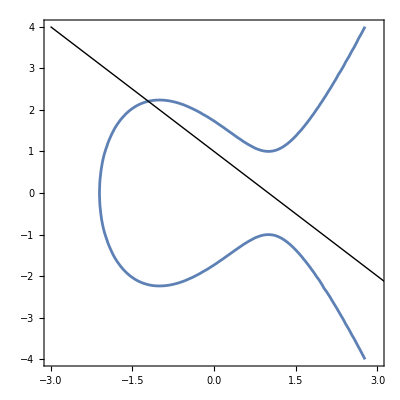

## Q3)

// we were asked to use contour plot to make the curve and then we were asked to have the first line as [{-3,-2},{4,4}]. We were told in the assignment to experiment with the placement of the second (vertical) line so that it intersects the curve and the first Line in the right way I tried doing that and I fount the best suitable line at [{2.63,-6},{2.63,6}] and then we were asked to experiment with the placement of a bullet so that it is reasonably close to the place that represents the addition of the two points of intersection
of the first Line with the curve. I did that below in the code with the point P + Q that I found at {2.63,-2.85} and have also marked it.

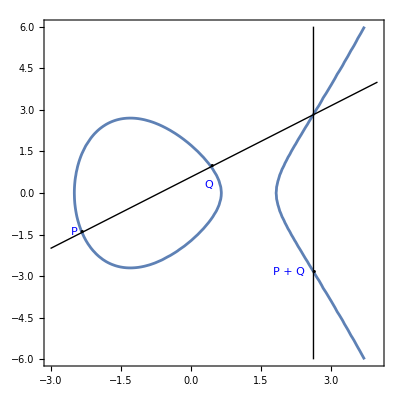

```mathematica
ContourPlot[y^2==x^3-5 x+3,{x,-3,4},{y,-6,6},Axes->True,Epilog->{Line[{{-3,-2},{4,4}}],Line[{{2.63,-6},{2.63,6}}],Text[Style["P + Q",FontColor->RGBColor[0,0,1]],{2.1,-2.85}],Text[Style["P",FontColor->RGBColor[0,0,1]],{-2.5,-1.4}],Text[Style["Q",FontColor->RGBColor[0,0,1]],{0.39,0.3}],Text["•",{-2.33,-1.4}],Text["•",{0.44,0.97}],Text["•",{2.63,-2.85}]}]
```

## Q4)

// we were just asked to remove the Flatten function that was given in the book and just solve it  with the table function.

```mathematica
Clear[x,y];
p=11;
Table[Solve[{y^2==x^3-5 x+3,x==u},{x,y},Modulus->p],{u,0,p-1}]
```

{{{x→0,y→5},{x→0,y→6}},{},{{x→2,y→1},{x→2,y→10}},{{x→3,y→2},{x→3,y→9}},{{x→4,y→5},{x→4,y→6}},{{x→5,y→2},{x→5,y→9}},{},{{x→7,y→5},{x→7,y→6}},{},{{x→9,y→4},{x→9,y→7}},{}}

## Q5)

// I used the line y = x-1 and found the intersection with the curve by using the Solve function. pretty straightforward.

```mathematica
p=11;Solve[ {y^2==x^3-5 x+3,y==x- 1},{x,y},Modulus-> p]
```

{{x→2,y→1},{x→3,y→2},{x→7,y→6}}

## Q6)

```mathematica
EllipticAdd[p_,a_,b_,c_,P_List,Q_List]:=Module[{lam,x3,y3,P3},Which[P=={O},R=Q,Q=={O},R=P,P[[1]]!=Q[[1]],lam=Mod[(Q[[2]]-P[[2]]) PowerMod[Q[[1]]-P[[1]],-1,p],p];
x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
y3=Mod[-(lam (x3-P[[1]])+P[[2]]),p];
R={x3,y3},(P==Q)&&(P!={O}),lam=Mod[(3*P[[1]]^2+2 a*P[[1]]+b) PowerMod[2 P[[2]],-1,p],p];
x3=Mod[lam^2-a-P[[1]]-Q[[1]],p];
y3=Mod[-(lam (x3-P[[1]])+P[[2]]),p];
R={x3,y3},(P[[1]]==Q[[1]])&&(P[[2]]!=Q[[2]]),R={O}];R]
```

```mathematica
p =11
```

11

```mathematica
a = -5
```

-5

```mathematica
b=3
```

3

```mathematica
c=0
```

0

```mathematica
P = {2,1}
```

{2,1}

```mathematica
Q ={3,2}
```

{3,2}

```mathematica
EllipticAdd[p,a,b,P,Q]
```

{7,5}

## Q7)

// I have done several other parts here too which may have not been in the assignment question.

// the code was pretty much given in the book, just had to add the Table part here., if the elliptic add function gives us a 0 then it means it yields a point at infinity. and I’ve also written integer digits of 432.

```mathematica
p=863;a=100;b=10;c=1;x=121;y=517;Mod[y^2-(x^3+a*x^2+b*x+c),p]==0
```

True

```mathematica
FactorInteger[432]
IntegerDigits[432]
IntegerDigits[432,2]
IntegerDigits[432/2,2]
IntegerDigits[432/3,2]
```

{{2,4},{3,3}}

{4,3,2}

{1,1,0,1,1,0,0,0,0}

{1,1,0,1,1,0,0,0}

{1,0,0,1,0,0,0,0}

```mathematica
p=863;P=.;
a=100;b=10;c=1;
P[0]={121,517};
P[i_] := P[i] = EllipticAdd[p,a,b,c,P[i-1],P[i-1]];
Q=EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[8],P[7]],		 EllipticAdd[p,a,b,c,P[5],P[4]]]
EllipticAdd[p,a,b,c,EllipticAdd[p,a,b,c,P[7],P[6]],	 	EllipticAdd[p,a,b,c,P[4],P[3]]]
EllipticAdd[p,a,b,c,P[7],P[4]]
```

{O}

{19,0}

{341,175}

```mathematica
doublingTable=Table[P[i],{i,0,19}]
```

{{121,517},{630,588},{447,354},{69,852},{348,843},{539,467},{572,822},{124,198},{804,143},{363,372},{533,612},{579,214},{790,469},{348,20},{539,396},{572,41},{124,665},{804,720},{363,491},{533,251}}

## Q8)

// following the above example codes
Let Alice choose m_A=130 and Bob m_B=288. Then Q_A=(162,663) and Q_B=(341,688), as can be checked as follows :

```mathematica
QAlice=EllipticAdd[p,a,b,c,P[7],P[1]]
```

{162,663}

```mathematica
QBob=EllipticAdd[p,a,b,c,P[8],P[5]]
```

{341,688}

// alice can compute the common key K_(A,B) with the calculation K_(A,B)=m_A Q_B, where m_A=130 is her secret key. She finds:

```mathematica
QA[0]={341,688}
```

{341,688}

```mathematica
QA[i_]:=QA[i]=EllipticAdd[p,a,b,c,QA[i-1],QA[i-1]]
```

```mathematica
EllipticAdd[p,a,b,c,QA[7],QA[1]]
```

{341,688}

// Likewise, Bob can compute the common key K_(A,B) with the calculation K_(A,B)=m_B Q_A, where m_B=288 is his secret key. He also finds:

```mathematica
QB[0]={162,663}
```

{162,663}

```mathematica
QB[i_]:=QB[i]=EllipticAdd[p,a,b,c,QB[i-1],QB[i-1]]
```

```mathematica
EllipticAdd[p,a,b,c,QB[8],QB[5]]
```

{341,688}

// we can see here they both got the same output that is {341,688}. hence I  worked through the diffie hellman to find the answer.

## Q9)

```mathematica
FiniteFields
```

FiniteFields

```mathematica
z16=GF[2,4]
```

GF[2,4]

```mathematica
FullForm[%]
```

GF[2,4]

```mathematica
FieldIrreducible[z16,x]
```

FieldIrreducible[GF[2,4],x]

```mathematica
Characteristic[z16]
```

Characteristic[GF[2,4]]

```mathematica
ExtensionDegree[z16]
```

ExtensionDegree[GF[2,4]]

```mathematica
FieldSize[z16]
```

FieldSize[GF[2,4]]

```mathematica
dd=z16[{0,0,1,1}]
```

GF[2,4][{0,0,1,1}]

```mathematica
dd+dd
```

2 GF[2,4][{0,0,1,1}]

```mathematica
dd-dd
```

0

```mathematica
ee=z16[{1,1,0,0}]
```

GF[2,4][{1,1,0,0}]

```mathematica
dd ee
```

GF[2,4][{0,0,1,1}] GF[2,4][{1,1,0,0}]

```mathematica
dd/ee
```

(GF[2,4][{0,0,1,1}])/(GF[2,4][{1,1,0,0}])

// calculates the powers of dd from 0 to 15, using modular exponentiation to ensure the results are within the field.

```mathematica
dd =z16[{0,0,1,1}]
```

GF[2,4][{0,0,1,1}]

```mathematica
Table[{n,dd^n},{n,0,15}]
```

{{0,1},{1,GF[2,4][{0,0,1,1}]},{2,(GF[2,4][{0,0,1,1}])^2},{3,(GF[2,4][{0,0,1,1}])^3},{4,(GF[2,4][{0,0,1,1}])^4},{5,(GF[2,4][{0,0,1,1}])^5},{6,(GF[2,4][{0,0,1,1}])^6},{7,(GF[2,4][{0,0,1,1}])^7},{8,(GF[2,4][{0,0,1,1}])^8},{9,(GF[2,4][{0,0,1,1}])^9},{10,(GF[2,4][{0,0,1,1}])^10},{11,(GF[2,4][{0,0,1,1}])^11},{12,(GF[2,4][{0,0,1,1}])^12},{13,(GF[2,4][{0,0,1,1}])^13},{14,(GF[2,4][{0,0,1,1}])^14},{15,(GF[2,4][{0,0,1,1}])^15}}

```mathematica
TableForm[Table[{n,dd^n},{n,0,15}],TableHeadings->{None,{"Power","Value"}}]
```

Power | Value
0 | 1
1 | GF[2,4][{0,0,1,1}]
2 | (GF[2,4][{0,0,1,1}])^2
3 | (GF[2,4][{0,0,1,1}])^3
4 | (GF[2,4][{0,0,1,1}])^4
5 | (GF[2,4][{0,0,1,1}])^5
6 | (GF[2,4][{0,0,1,1}])^6
7 | (GF[2,4][{0,0,1,1}])^7
8 | (GF[2,4][{0,0,1,1}])^8
9 | (GF[2,4][{0,0,1,1}])^9
10 | (GF[2,4][{0,0,1,1}])^10
11 | (GF[2,4][{0,0,1,1}])^11
12 | (GF[2,4][{0,0,1,1}])^12
13 | (GF[2,4][{0,0,1,1}])^13
14 | (GF[2,4][{0,0,1,1}])^14
15 | (GF[2,4][{0,0,1,1}])^15

```mathematica
Table[{n,dd^n},{n,0,30}]
```

{{0,1},{1,GF[2,4][{0,0,1,1}]},{2,(GF[2,4][{0,0,1,1}])^2},{3,(GF[2,4][{0,0,1,1}])^3},{4,(GF[2,4][{0,0,1,1}])^4},{5,(GF[2,4][{0,0,1,1}])^5},{6,(GF[2,4][{0,0,1,1}])^6},{7,(GF[2,4][{0,0,1,1}])^7},{8,(GF[2,4][{0,0,1,1}])^8},{9,(GF[2,4][{0,0,1,1}])^9},{10,(GF[2,4][{0,0,1,1}])^10},{11,(GF[2,4][{0,0,1,1}])^11},{12,(GF[2,4][{0,0,1,1}])^12},{13,(GF[2,4][{0,0,1,1}])^13},{14,(GF[2,4][{0,0,1,1}])^14},{15,(GF[2,4][{0,0,1,1}])^15},{16,(GF[2,4][{0,0,1,1}])^16},{17,(GF[2,4][{0,0,1,1}])^17},{18,(GF[2,4][{0,0,1,1}])^18},{19,(GF[2,4][{0,0,1,1}])^19},{20,(GF[2,4][{0,0,1,1}])^20},{21,(GF[2,4][{0,0,1,1}])^21},{22,(GF[2,4][{0,0,1,1}])^22},{23,(GF[2,4][{0,0,1,1}])^23},{24,(GF[2,4][{0,0,1,1}])^24},{25,(GF[2,4][{0,0,1,1}])^25},{26,(GF[2,4][{0,0,1,1}])^26},{27,(GF[2,4][{0,0,1,1}])^27},{28,(GF[2,4][{0,0,1,1}])^28},{29,(GF[2,4][{0,0,1,1}])^29},{30,(GF[2,4][{0,0,1,1}])^30}}

```mathematica
Z2mEllipticAdd[a_,c_,P_List,Q_List]:=Module[{lam,x3,y3,P3,R},Which[P=={O},R=Q,Q=={O},R=P,ToElementCode[P[[1]]]!=ToElementCode[Q[[1]]],lam=(Q[[2]]+P[[2]])/(Q[[1]]+P[[1]]);
x3=lam^2+lam+a+P[[1]]+Q[[1]];
y3=lam (x3+P[[1]])+x3+P[[2]];
R={x3,y3},((ToElementCode[P[[1]]]==ToElementCode[Q[[1]]])&&(ToElementCode[P[[2]]]==ToElementCode[Q[[2]]]))&&(P!={O}),lam=P[[1]]+P[[2]]/P[[1]];
x3=lam^2+lam+a;
y3=P[[1]]^2+(lam+1) x3;
R={x3,y3},(ToElementCode[P[[1]]]==ToElementCode[Q[[1]]])&&(ToElementCode[P[[2]]]!=ToElementCode[Q[[2]]]),R={O}];R];

a=ee;c=0; (*Replace `ee` with the actual value*)
P[0]={x,y};
```

```mathematica
PDoubles=Table[P[i]=Z2mEllipticAdd[a,c,P[i-1],P[i-1]],{i,0,31}]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

{TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit],TerminatedEvaluation[RecursionLimit]}

```mathematica
QAlice=Z2mEllipticAdd[a,c,PDoubles[[3]],PDoubles[[1]]]
```

Part::partd: Part specification PDoubles⟦3⟧ is longer than depth of object.

Part::partd: Part specification PDoubles⟦1⟧ is longer than depth of object.

```mathematica
Z2mEllipticAdd[ee,0,PDoubles⟦3⟧,PDoubles⟦1⟧]
```

Part::partd: Part specification PDoubles⟦3⟧ is longer than depth of object.

Part::partd: Part specification PDoubles⟦1⟧ is longer than depth of object.

Z2mEllipticAdd[ee,0,PDoubles⟦3⟧,PDoubles⟦1⟧]

# Week 5

## Q1)

// BB84 QKD protocol
first we made Alice basis my using random integer and similarly we made alice data and bob basis using it :

```mathematica
AliceBasis=RandomInteger[{0,1},40]
```

{0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,1}

```mathematica
AliceData=RandomInteger[{0,1},40]
```

{1,1,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,0,1,0,0,0,1,0,0,1}

```mathematica
BobBasis=RandomInteger[{0,1},40]
```

{0,1,0,0,0,1,0,1,0,1,1,1,1,0,0,0,0,1,0,0,0,1,0,1,1,1,0,1,0,1,0,0,1,1,0,0,1,1,1,1}

// it was told that To model Bob’s measurements of the data, set BobData to a list of 0 and 1 of length 40, such that at each position, if AliceBasis and BobBasis
are equal, then BobData agrees with AliceData, else is random. So, I simply made the if condition for it saying if it matches then bob data = alice data if not then bob data = random integer.

```mathematica
BobData=Table[If[AliceBasis[[i]]==BobBasis[[i]],AliceData[[i]],RandomInteger[{0,1}]],{i,1,40}]
```

{1,0,1,0,0,1,1,1,1,0,0,1,0,1,1,0,0,0,1,0,0,1,1,1,0,1,0,1,1,0,1,0,1,0,0,0,1,0,1,1}

// then it was said to model the exchange of basis information, set EqualBases to 1 at each position where AliceBasis equals BobBasis, and 0 otherwise:

```mathematica
EqualBases=Table[If[AliceBasis[[i]]==BobBasis[[i]],1,0],{i,1,40}]
```

{1,0,0,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,1,1,0,1,0,0,1,0,1,1,1,0,1,1,0,0,0,1}

// then it was said using a For loop and Append, set AgreedDataAlice to be the sublist of Alice’s data selected on positions where EqualBases equals 1. Similarly, set AgreedDataBob to be the sublist of Bob’s data selected on positions where EqualBases equals 1. Output AgreedDataAlice and AgreedDataBob. to append the data in the list of AgreedDataAlice and Bob I firstly made them as empty { } and then used a for look to check the above condition, if the condition was true simply just used AppendTo function to add the data to that list. I could have made two different for loops, but the condition was same for both of them it would have just taken more time so made them into single.

```mathematica
AgreedDataAlice={}
```

{}

```mathematica
AgreedDataBob={}
```

{}

// COULD HAVE MADE THIS USING 2 FOR LOOPS.

```mathematica
For[i=1,i<=40,i++,If[EqualBases[[i]]==1,AppendTo[AgreedDataAlice,AliceData[[i]]];
AppendTo[AgreedDataBob,BobData[[i]]]]];
```

// then it was said using another For loop and Random[Integer], partition AgreedDataAlice and AgreedDataBob into the set of agreed key bits and the set of agreed check bits: AgreedKeyAlice, AgreedKeyBob, CheckDigitsAlice,
CheckDigitsBob, and output these four sequences

```mathematica
AgreedKeyAlice={}
```

{}

```mathematica
AgreedKeyBob={}
```

{}

```mathematica
CheckDigitsAlice={}
```

{}

```mathematica
CheckDigitsBob={}
```

{}

// I’m gonna fully explain what each part of this For Loop is actually doing,

 For[i = 1, i <= Length[AgreedDataAlice], i++]: This loop iterates over each bit in the AgreedDataAlice list. Since AgreedDataAlice and AgreedDataBob have the same length, this loop effectively iterates over both lists simultaneously.

IIf[EvenQ[i] : This condition checks if the current index i is even. If it is even, it means we’re dealing with a check bit.

this is for the key bit , basically odd index :
AppendTo[AgreedKeyAlice, AgreedDataAlice[[i]]]: Appends the current bit from AgreedDataAlice to the AgreedKeyAlice list. AppendTo[AgreedKeyBob, AgreedDataBob[[i]]]: Appends the corresponding bit from AgreedDataBob to the AgreedKeyBob list.

this is for check bit, even index :
AppendTo[CheckDigitsAlice, AgreedDataAlice[[i]]]: Appends the current bit from AgreedDataAlice to the CheckDigitsAlice list. AppendTo[CheckDigitsBob, AgreedDataBob[[i]]]: Appends the corresponding bit from AgreedDataBob to the CheckDigitsBob list.

I could have also used another code which basically checks if the digits are odd instead of even. - 

 For[i = 1, i <= Length[AgreedDataAlice], i++,
  If[Mod[i, 2] == 1, 
    AppendTo[AgreedKeyAlice, AgreedDataAlice[[i]]];
    AppendTo[AgreedKeyBob, AgreedDataBob[[i]]]
  ] Else[
    AppendTo[CheckDigitsAlice, AgreedDataAlice[[i]]];
    AppendTo[CheckDigitsBob, AgreedDataBob[[i]]]
  ]
];

```mathematica
For[i=1,i<=Length[AgreedDataAlice],i++,If[EvenQ[i],AppendTo[CheckDigitsAlice,AgreedDataAlice[[i]]];
AppendTo[CheckDigitsBob,AgreedDataBob[[i]]];,AppendTo[AgreedKeyAlice,AgreedDataAlice[[i]]];
AppendTo[AgreedKeyBob,AgreedDataBob[[i]]];];];
```

```mathematica
Print["AliceBasis:",AliceBasis];
Print["AliceData:",AliceData];
Print["BobBasis:",BobBasis];
Print["BobData:",BobData];
Print["EqualBases:",EqualBases];
Print["AgreedDataAlice:",AgreedDataAlice];
Print["AgreedDataBob:",AgreedDataBob];
Print["AgreedKeyAlice:",AgreedKeyAlice];
Print["AgreedKeyBob:",AgreedKeyBob];
Print["CheckDigitsAlice:",CheckDigitsAlice];
Print["CheckDigitsBob:",CheckDigitsBob];
```

AliceBasis:{0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,1,1,0,1,0,0,0,0,1,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,1}

AliceData:{1,1,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,0,1,0,0,0,1,0,0,1}

BobBasis:{0,1,0,0,0,1,0,1,0,1,1,1,1,0,0,0,0,1,0,0,0,1,0,1,1,1,0,1,0,1,0,0,1,1,0,0,1,1,1,1}

BobData:{1,0,1,0,0,1,1,1,1,0,0,1,0,1,1,0,0,0,1,0,0,1,1,1,0,1,0,1,1,0,1,0,1,0,0,0,1,0,1,1}

EqualBases:{1,0,0,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,1,1,0,1,0,0,1,0,1,1,1,0,1,1,0,0,0,1}

AgreedDataAlice:{1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1}

AgreedDataBob:{1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1}

AgreedKeyAlice:{1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1}

AgreedKeyBob:{1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,0,1,0,1,1,0,0,1}

CheckDigitsAlice:{1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0}

CheckDigitsBob:{1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,1,0,1,0,0,1,1,0,0,1,1,1,1,1,0,1,0,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0}

// basically printed every result as the assignment asked that they wanted output for everything.

## Q2)

// B92 QKD Protocol :

 we were told to set AliceData to a random list of 0 and 1 of length 40. Since in B92, the basis for transmission is chosen according to the data, set AliceBasis to be a copy of AliceData. and also set Set BobBasis to be a random list of 0 and 1 of length 40.

```mathematica
AliceData=RandomInteger[{0,1},40]
```

{0,1,1,1,0,1,0,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,1,1,0,1,0,1,1,0,0}

```mathematica
AliceBasis=AliceData
```

{0,1,1,1,0,1,0,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,1,1,0,1,0,1,1,0,0}

```mathematica
BobBasis=RandomInteger[{0,1},40]
```

{0,1,0,0,1,1,1,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,0,1,0,0,0,1,0,0}

// To model Bob’s measurements of the data,we were told to  set BobData to a list of 0 and 1 of length 40, such that at each position, if AliceBasis and BobBasis are equal, then BobData agrees with AliceData, else is random

```mathematica
BobData=Table[If[AliceBasis[[i]]==BobBasis[[i]],AliceData[[i]],RandomInteger[{0,1}]],{i,1,40}]
```

{0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,1,0,0,1,0,0,0,0,1,1,1,1,0,1,1,0,0}

//reliable data reflects the positions where Bob can trust the value he measures because he and Alice used the same basis for those qubits.

```mathematica
ReliableData=Table[If[AliceBasis[[i]]==BobBasis[[i]],1,0],{i,Length[AliceBasis]}]
```

{1,1,0,0,0,1,0,0,0,1,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,1,0,1,1,1}

// using a For loop and Append, set AgreedDataAlice to be the sublist of Alice’s data selected on those positions in which ReliableData equals 1.Similarly, set AgreedDataBob to be the
sublist of Bob’s data selected on positions where ReliableData equals 1. I’ve made this in one loop, could have used 2 loops here too.

```mathematica
AgreedDataAlice={};
AgreedDataBob={};
For[i=1,i<=40,i++,If[ReliableData[[i]]==1,AppendTo[AgreedDataAlice,AliceData[[i]]];
AppendTo[AgreedDataBob,BobData[[i]]];];];
```

```mathematica
AgreedKeyAlice={}
AgreedKeyBob={}
CheckDigitsAlice={}
CheckDigitsBob={}
```

{}

{}

{}

«1 more identical outputs»

// this step is similar to the previous example so I’ll not explain this again.

```mathematica
For[i=1,i<=Length[AgreedDataAlice],i++,If[EvenQ[i],AppendTo[CheckDigitsAlice,AgreedDataAlice[[i]]];
AppendTo[CheckDigitsBob,AgreedDataBob[[i]]];,AppendTo[AgreedKeyAlice,AgreedDataAlice[[i]]];
AppendTo[AgreedKeyBob,AgreedDataBob[[i]]];];];
```

```mathematica
Print["AliceBasis:",AliceBasis];
Print["AliceData:",AliceData];
Print["BobBasis:",BobBasis];
Print["BobData:",BobData];
Print["ReliableData:",ReliableData];
Print["AgreedDataAlice:",AgreedDataAlice];
Print["AgreedDataBob:",AgreedDataBob];
Print["AgreedKeyAlice:",AgreedKeyAlice];
Print["AgreedKeyBob:",AgreedKeyBob];
Print["CheckDigitsAlice:",CheckDigitsAlice];
Print["CheckDigitsBob:",CheckDigitsBob];
```

AliceBasis:{0,1,1,1,0,1,0,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,1,1,0,1,0,1,1,0,0}

AliceData:{0,1,1,1,0,1,0,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,1,1,0,1,0,1,1,0,0}

BobBasis:{0,1,0,0,1,1,1,0,0,0,1,1,0,1,1,1,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,0,1,0,0,0,1,0,0}

BobData:{0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,0,1,0,1,0,1,1,0,0,1,0,0,0,0,1,1,1,1,0,1,1,0,0}

ReliableData:{1,1,0,0,0,1,0,0,0,1,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,1,0,1,1,1}

AgreedDataAlice:{0,1,1,0,1,1,1,1,0,0,0,0,0,1,0,1,0,0}

AgreedDataBob:{0,1,1,0,1,1,1,1,0,0,0,0,0,1,0,1,0,0}

AgreedKeyAlice:{0,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0}

AgreedKeyBob:{0,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0}

CheckDigitsAlice:{1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0}

CheckDigitsBob:{1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0}

## Q3)

// As before, using Table and Random[Integer], set AliceBasis and BobBasis to random lists of 0 and 1 and To model the data positions that Eve interferes with, set EvesDrop to a random list of 0 and 1

```mathematica
AliceBasis=Table[RandomInteger[{0,1}],{60}];
BobBasis=Table[RandomInteger[{0,1}],{60}];
EvesDrop=Table[RandomInteger[{0,1}],{60}];
```

// To model the exchange of basis information, set EqualBases to 1 at each position where AliceBasis equals BobBasis and 0 otherwise.

```mathematica
EqualBases=Table[If[AliceBasis[[i]]==BobBasis[[i]],1,0],{i,60}];
```

// Since we know in advance when Eve will be eves dropping, set ReliableData to a table with 1 at each position where EqualBases is 1 and EvesDrop is 0

```mathematica
ReliableData=Table[If[EqualBases[[i]]==1&&EvesDrop[[i]]==0,1,0],{i,60}];
```

// basically created AliceData and BoboData that is to be changed in the coming for loop, so just made with with zeros for now.

```mathematica
AliceData=Table[0,{60}];
BobData=Table[0,{60}];
```

// Now we model the measurement of entangled states. When the entangled data (which we do not represent, we only model its measurement) is not interfered with, Alice and Bob measure a random bit, but always the same random bit. When there is interference, the bits measured by Alice and Bob are uncorrelated random bits. Using a For loop, set AliceData and BobData to lists of random bits which must be the same at each position where ReliableData is 1

```mathematica
For[i=1,i<=60,i++,If[ReliableData[[i]]==1,AliceData[[i]]=BobData[[i]]=RandomInteger[{0,1}],AliceData[[i]]=RandomInteger[{0,1}];
BobData[[i]]=RandomInteger[{0,1}];];];
```

// again made 2 list AgreedDataAlice and AgreedDataBob and will Set AgreedDataAlice to be the sublist of Alice’s data selected on those positions in which EqualBases is 1. Similarly, set AgreedDataBob to be the sublist of Bob’s data selected on positions where EqualBases is 1

```mathematica
AgreedDataAlice={};
AgreedDataBob={};
For[i=1,i<=60,i++,If[EqualBases[[i]]==1,AppendTo[AgreedDataAlice,AliceData[[i]]];
AppendTo[AgreedDataBob,BobData[[i]]];];];
```

// this step now is the same as question 1 of this week so not gonna explain it again here.

```mathematica
AgreedKeyAlice={};
AgreedKeyBob={};
CheckDigitsAlice={};
CheckDigitsBob={};

For[i=1,i<=Length[AgreedDataAlice],i++,If[EvenQ[i],AppendTo[CheckDigitsAlice,AgreedDataAlice[[i]]];
AppendTo[CheckDigitsBob,AgreedDataBob[[i]]];,AppendTo[AgreedKeyAlice,AgreedDataAlice[[i]]];
AppendTo[AgreedKeyBob,AgreedDataBob[[i]]];];];
```

```mathematica
Print["AliceBasis:",AliceBasis];
Print["BobBasis:",BobBasis];
Print["EvesDrop:",EvesDrop];
Print["ReliableData:",ReliableData];
Print["AliceData:",AliceData];
Print["BobData:",BobData];
Print["AgreedDataAlice:",AgreedDataAlice];
Print["AgreedDataBob:",AgreedDataBob];
Print["AgreedKeyAlice:",AgreedKeyAlice];
Print["AgreedKeyBob:",AgreedKeyBob];
Print["CheckDigitsAlice:",CheckDigitsAlice];
Print["CheckDigitsBob:",CheckDigitsBob];
```

AliceBasis:{1,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,0,0,0,1,1,1,1,0,1,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,1,0,1,1,1,1,0,0,0,0,0,1,0,0,1}

BobBasis:{1,1,1,0,1,0,0,0,1,1,0,0,1,1,1,1,0,1,1,1,1,1,1,1,1,0,0,1,1,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,1,1,1,0,0,1,1,1,1,0,0,1,0}

EvesDrop:{0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0}

ReliableData:{1,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0}

AliceData:{1,0,0,0,1,0,0,1,0,1,1,1,1,1,0,0,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,1,0,1,0,0,0,0,1,1,0,1,0,1,1,1,0,1,0,0,1,1,1,0,0,1,0,0,1,0}

BobData:{1,0,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,0,1,1,0,0,1,0,0,1,0,1,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0,0,0,0}

AgreedDataAlice:{1,0,0,0,0,1,1,0,1,1,1,0,0,0,1,0,1,0,0,0,1,1,1,1,1,0,0,1,0}

AgreedDataBob:{1,0,0,1,0,0,1,0,1,1,1,0,0,0,1,1,0,0,1,0,1,1,0,1,1,0,1,0,0}

AgreedKeyAlice:{1,0,0,1,1,1,0,1,1,0,1,1,1,0,0}

AgreedKeyBob:{1,0,0,1,1,1,0,1,0,1,1,0,1,1,0}

CheckDigitsAlice:{0,0,1,0,1,0,0,0,0,0,1,1,0,1}

CheckDigitsBob:{0,1,0,0,1,0,0,1,0,0,1,1,0,0}